```mathematica
ConstructMarkovMap[seqs_ ,numBack_ ,autoEnd_]:=Module[{elems=DeleteDuplicates[Flatten[seqs,1]],map=<||>,corrs=Flatten[Table[Take[#,{k,k+numBack}],{k,1,Length[#]-numBack}]&/@If[autoEnd,Append[#,seqs]&/@seqs,seqs],1],i,key,val},
For[i=1,i≤Length[corrs],++i,
key=corrs[[i]][[1;;-2]];
val=corrs[[i]][[-1]];
map[key]=If[KeyExistsQ[map,key],
Append[map[key],val],
{val}
];
];
Return[map];
];
MarkovTrain[seqs_,numBack_,autoEnd_]:=Table[ConstructMarkovMap[seqs,i,autoEnd],{i,numBack}];
MarkovGenerate[seqs_ ,maps_,maxlength_:0]:=Module[{elemsrpt=Flatten[seqs,1],numBack=Length[maps],elems,i,outSeq,next},
elems=DeleteDuplicates[elemsrpt];
outSeq={RandomChoice[If[Length[seqs]==1,elemsrpt,First/@seqs]]};
For[i=1,i<numBack,++i,
next=RandomChoice[Lookup[maps[[i]],Key[outSeq[[1;;i]]],elemsrpt]];
If[next==seqs,Return[outSeq]];
outSeq=Append[outSeq,next];
];
For[i=numBack,maxlength≤0||i<maxlength,++i,
next=RandomChoice[Lookup[maps[[-1]],Key[outSeq[[i-numBack+1;;i]]],elemsrpt]];
If[next==seqs,Return[outSeq]];
outSeq=Append[outSeq,next];
];
Return[outSeq];
];
Markov[seqs_,numBack_,maxLength_:0,autoEnd_:True]:=MarkovGenerate[seqs,MarkovTrain[seqs,numBack,autoEnd||maxLength≤0],maxLength];
DeRawifyText[text_]:=DeleteCases[StringSplit[text//ToLowerCase,{Whitespace,(x:RegularExpression["[!\"#$%&()*+,
 \\-./:;<=>?@
 [\\\\\\]^_`{|}~]"]):>x}],""];
DeRawifyMusic[musicRaw_]:=Module[{music={},sorted,i,duration,minendt},
sorted=SortBy[GatherBy[musicRaw,#[[2,1]]&],#[[1,2,1]]&];
For[i=1,i≤Length[sorted],++i,
minendt=#[[2,2]]&/@sorted[[i]]//Min;
duration=-sorted[[i,1,2,1]]+Min[If[i<Length[sorted],#[[1,2,1]]&/@Take[sorted,{i+1,-1}],{}],minendt];
music=Append[music,SoundNote[#[[1]]&/@sorted[[i]],duration]];
If[i<Length[sorted],
duration=sorted[[i+1,1,2,1]]-minendt;
If[duration>0,music=Append[music,SoundNote[None,duration]]];
];
];
Return[music];
];
MarkovWordTrain[words_,numBack_,autoEnd_:True]:=MarkovTrain[Characters/@words,numBack,autoEnd];
MarkovWordGenerate[words_,maps_,maxLength_:0]:=MarkovGenerate[Characters/@words,maps,maxLength]//StringJoin;
MarkovWord[words_,numBack_,maxLength_:0,autoEnd_:True]:=Markov[Characters/@words,numBack,maxLength,autoEnd]//StringJoin;
MarkovTextTrain[text_,numBack_,autoEnd_:True]:=MarkovTrain[DeRawifyText/@text,numBack,autoEnd];
MarkovTextGenerate[text_,maps_,maxLength_:0]:=Riffle[MarkovGenerate[DeRawifyText/@text,maps,maxLength]," "]//StringJoin;
MarkovText[text_,numBack_,maxLength_:0,autoEnd_:True]:=Riffle[Markov[DeRawifyText/@text,numBack,maxLength,autoEnd]," "]//StringJoin;
MarkovMusicTrain[music_,numBack_,autoEnd_:True]:=MarkovTrain[DeRawifyMusic/@music,numBack,autoEnd];
MarkovMusicGenerate[music_,maps_,maxLength_:0]:=MarkovGenerate[DeRawifyMusic/@music,maps,maxLength]//Sound;
MarkovMusic[music_,numBack_,maxLength_:0,autoEnd_:True]:=Markov[DeRawifyMusic/@music,numBack,maxLength,autoEnd]//Sound;
```

```mathematica
reddit[sub_,pages_:10]:=Module[{posts={},data,after},
data=("data"/.Import["https://www.reddit.com/r/"<>sub<>"/top/.json?t=all","JSON"]);
posts="selftext"/.("data"/.("children"/.data));
Do[
after="after"/.data;
data=("data"/.Import["https://www.reddit.com/r/"<>sub<>"/top/.json?t=all&count=25&after="<>after,"JSON"]);
posts=Join[posts,"selftext"/.("data"/.("children"/.data))];
,{pages-1}];
DeleteCases[posts,""]
];
```

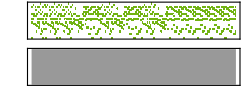
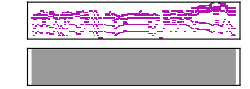
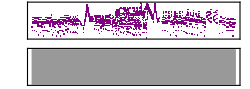
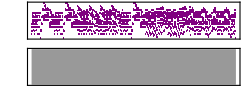
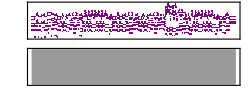
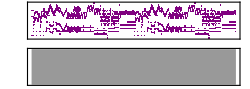
```mathematica
matrixtext=Import["http://pastebin.com/raw.php?i=cYrKU6Sv","Text"];
hotelcalifornialyrics=Import["http://pastebin.com/raw.php?i=rCJPwhRr","Text"];
greentext=Import["http://pastebin.com/raw.php?i=ft0KLq7b","Text"];
navyseals=StringSplit[Import["http://pastebin.com/raw.php?i=NggVMMxg","Text"],"\n"];
penguin=StringSplit[Import["http://pastebin.com/raw.php?i=QpR5xCT7","Text"],";;;"];
copypasta=reddit["circlejerkcopypasta"]~Join~reddit["copypasta"];
badhistory=reddit["badhistory"];
dongerino=reddit["raiseyourdongers"];
hundredwords={"the","be","to","of","and","a","in","that","have","I","it","for","not","on","with","he","as","you","do","at","this","but","his","by","from","they","we","say","her","she","or","an","will","my","one","all","would","there","their","what","so","up","out","if","about","who","get","which","go","me","when","make","can","like","time","no","just","him","know","take","people","into","year","your","good","some","could","them","see","other","than","then","now","look","only","come","its","over","think","also","back","after","use","two","how","our","work","first","well","way","even","new","want","because","any","these","give","day","most","us"};
thousandwords=StringSplit[Import["http://pastebin.com/raw.php?i=GaZyTfwv","Text"]];
dongerini=StringSplit[Import["http://pastebin.com/raw/AeSpDvwD","Text"],"\n"];
hotelcaliforniamusic=-Graphics-[[1]];
marseillaisemusic=-Graphics-[[1]];
liebestraummusic=-Graphics-[[1]];
mapleleafragmusic=-Graphics-[[1]];
mistymountainmusic=-Graphics-[[1]];
rogueportmusic=-Graphics-[[1]];
```

```mathematica
DeRawifyMusic[hotelcaliforniamusic]//Sound
DeRawifyMusic[marseillaisemusic]//Sound
DeRawifyMusic[liebestraummusic]//Sound
DeRawifyMusic[mapleleafragmusic]//Sound
DeRawifyMusic[mistymountainmusic]//Sound
```

```mathematica
MarkovText[{matrixtext},1,250,False]
```

```mathematica
MarkovText[{hotelcalifornialyrics},1,250,False]
```

```mathematica
MarkovText[{greentext},1,250,False]
```

```mathematica
MarkovText[navyseals,2]
```

```mathematica
MarkovText[penguin,2]
```

```mathematica
MarkovText[copypasta,2]
```

```mathematica
MarkovText[badhistory,2,200]
```

```mathematica
MarkovText[navyseals~Join~Flatten[ConstantArray[penguin,Length[navyseals]/Length[penguin]//Floor],1],2]
```

```mathematica
MarkovText[StringReplace[navyseals,{"couldn't"->"could not","wouldn't"->"would not","didn't"->"did not"}]~Join~ConstantArray[greentext,Length[navyseals]/2//Floor],2]
```

```mathematica
MarkovWord[{matrixtext},10, 500]
```

```mathematica
MarkovWord[hundredwords,1]
```

```mathematica
thousandwordmaps=MarkovWordTrain[thousandwords,2];
DeleteCases[Table[MarkovWordGenerate[thousandwords,thousandwordmaps],{100}],x_/;StringLength[x]≤2||Count[thousandwords,x]>0]
```

```mathematica
MarkovMusic[{hotelcaliforniamusic},1,250,False]
```

```mathematica
MarkovMusic[{marseillaisemusic},1,250,False]
```

```mathematica
MarkovMusic[{liebestraummusic},1,250,False]
```

```mathematica
MarkovMusic[{mapleleafragmusic},1,250,False]
```

```mathematica
MarkovMusic[{mistymountainmusic},1,250,False]
```

```mathematica
MarkovMusic[{rogueportmusic},1]
```

```mathematica
dongertrain=MarkovWordTrain[dongerini,1];
Table[MarkovWordGenerate[dongerini,dongertrain],{100}]//MatrixForm
```